```mathematica
(*cell sizes*)
rightcell[n_,k_,j_]:=Sum[(-1)^(r)*Binomial[k-j,r]*((k-r+1)/(2n+k-r+1))*Binomial[2n+k-r+1,n],{r,0,k-j}]
```

```mathematica
FullSimplify[rightcell[n,k,j]]
```

1/(1+k+2 n)(1+k) Binomial[1+k+2 n,n] Hypergeometric2F1[j-k,-1-k-n,-k-2 n,1]+1/(k+2 n)(-j+k) Binomial[k+2 n,n] Hypergeometric2F1[1+j-k,-k-n,1-k-2 n,1]

```mathematica
simplifiedrightcell[n_,k_,j_]:=((1+k)*Binomial[1+k+2*n,n]/(1+k+2*n))*(Product[n-r,{r,1,k-j}]/Product[2*n+k-r,{r,0,k-j-1}])+((k-j)*Binomial[k+2*n,n]/(k+2*n))*(Product[n-r,{r,1,k-j-1}]/Product[-1+k+2*n-r,{r,0,k-j-2}])
```

```mathematica
FullSimplify[simplifiedrightcell[n,k,j]]
```

((1-j+2 k) Gamma[1+j+2 n])/(Gamma[1+j-k+n] Gamma[2+k+n])

```mathematica
leftcell[n_,k_,j_]:=Sum[(-1)^(r)*Binomial[k-j+1,r]*((k-r+1)/(2n+k-r+3))*Binomial[2n+k-r+3,n+1],{r,0,k-j+1}]
```

```mathematica
FullSimplify[leftcell[n,k,j]]
```

1/(3+k+2 n)(1+k) Binomial[3+k+2 n,1+n] Hypergeometric2F1[-1+j-k,-2-k-n,-2-k-2 n,1]+1/(2+k+2 n)(1-j+k) Binomial[2+k+2 n,1+n] Hypergeometric2F1[j-k,-1-k-n,-1-k-2 n,1]

```mathematica
simplifiedleftcell[n_,k_,j_]:=((1+k)*Binomial[3+k+2*n,1+n]/(3+k+2*n))*(Pochhammer[n-k+j,k-j+1]/Pochhammer[2n+j+2,k-j+1])+((k-j+1)*Binomial[2+k+2*n,1+n]/(2+k+2*n))*(Pochhammer[n-k+j+1,k-j]/Pochhammer[2n+j+2,k-j])
```

```mathematica
FullSimplify[simplifiedleftcell[n,k,j]]
```

((2-j+2 k) Gamma[2+j+2 n])/(Gamma[1+j-k+n] Gamma[3+k+n])

```mathematica
(*Stirling Approximation*)
approx[n_]:=Sqrt[2*Pi*n]*(n/E)^n
```

```mathematica
(*upper bound of right cell asymptotic*)
FullSimplify[Asymptotic[((1-j+2 k) Gamma[1+j+2 n])/(Gamma[1+j-k+n] Gamma[2+k+n]),n->Infinity]]
```

(2^(j+2 n) (1-j+2 k))/(n^(3/2) √π)

```mathematica
(*lower bound of right cell asymptotic - using Stirling's Approximation*)
FullSimplify[Asymptotic[((1-j+2 k) approx[j+2 n])/(approx[j-k+n] approx[1+k+n]),n->Infinity]]
```

(2^(j+2 n) ⅇ^(-(j+j^2-4 j k+4 (1+k+k^2))/(4 n)) (1-j+2 k))/(n^(3/2) √π)

```mathematica
(*plot of right cell size for j=0 and n=100 to truncate*)
DiscretePlot[rightcell[100,k,0],{k,0,100},PlotRange->All,GridLines->{{{2*Sqrt[2*100],Thick}},{}}]
```

-Graphics-

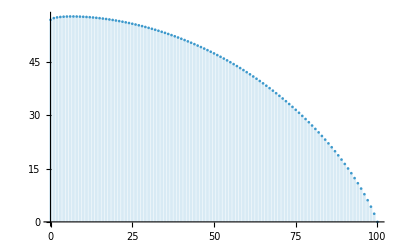

```mathematica
(*Log10 version*)
DiscretePlot[Log10[rightcell[100,k,0]],{k,0,100},PlotRange->All,GridLines->{{{2*Sqrt[2*100],Thick}},{}}]
```

```mathematica
(*upper bound of size of truncated monoid*)
```

```mathematica
(*use Stirling approximation on summand in double sum for size of monoid*)
FullSimplify[Binomial[k+1,2j+1]*(((1-j+2 k) approx[j+2 n])/(approx[j-k+n] approx[1+k+n]))*(((2-j+2 k) approx[1+j+2 n])/(approx[j-k+n] approx[2+k+n]))]
```

1/(2 π)ⅇ^2 (-1+j-2 k) (j-2 (1+k)) (j-k+n)^(-1-2 (j-k+n)) (1+k+n)^(-3/2-k-n) (2+k+n)^(-5/2-k-n) (j+2 n)^(1/2+j+2 n) (1+j+2 n)^(3/2+j+2 n) Binomial[1+k,1+2 j]

```mathematica
(*estimate by taking the asymptotic of the summand*)
FullSimplify[Asymptotic[1/(2 π)ⅇ^2 (-1+j-2 k) (j-2 (1+k)) (j-k+n)^(-1-2 (j-k+n)) (1+k+n)^(-3/2-k-n) (2+k+n)^(-5/2-k-n) (j+2 n)^(1/2+j+2 n) (1+j+2 n)^(3/2+j+2 n) Binomial[1+k,1+2 j],n->Infinity]]
```

(2^(1+2 j+4 n) ⅇ^(-(7+(j-2 k)^2+6 k)/(2 n)) (-1+j-2 k) (j-2 (1+k)) Binomial[1+k,1+2 j])/(n^3 π)

```mathematica
(*ⅇ^(-(7+(j-2 k)^2+6 k)/(2 n)) is maximal when j=k=0, so we have an upper bound*)
FullSimplify[Sum[(2^(1+2 j+4 n) ⅇ^(-7/(2 n)) (-1+j-2 k) (j-2 (1+k)) Binomial[1+k,1+2 j])/(n^3 π),{j,0,Floor[k/2]}]]
```

(2^(-3+4 n) ⅇ^(-7/2/n) (3 (-1)^k (1+6 k+4 k^2)+3^k (93+2 k (101+50 k))))/(3 n^3 π)

```mathematica
FullSimplify[Sum[(2^(-3+4 n) ⅇ^(-7/2/n) (3 (-1)^k (1+6 k+4 k^2)+3^k (93+2 k (101+50 k))))/(3 n^3 π),{k,0,2*Sqrt[2n]}]]
```

(4^(-1+2 n) ⅇ^(-7/2/n) (-8+(-1)^(2 √2 √n)+5 (-1)^(2 √2 √n) √2 √n+8 (-1)^(2 √2 √n) n+9^(√2 √n) (23+51 √2 √n+200 n)))/(n^3 π)

```mathematica
(*get the asymptotic of the numerator then divide by denominator*)
FullSimplify[Asymptotic[4^(-1+2 n) ⅇ^(-7/2/n) (-8+(-1)^(2 √2 √n)+5 (-1)^(2 √2 √n) √2 √n+8 (-1)^(2 √2 √n) n+9^(√2 √n) (23+51 √2 √n+200 n)),n->Infinity]/(n^3 π)]
```

(25 2^(1+4 n) 9^(√2 √n))/(n^2 π)

```mathematica
(*limit of nth root*)
Limit[((25 2^(1+4 n) 9^(√2 √n))/(n^2 π))^(1/n),n->Infinity]
```

16

```mathematica
(*alternate method:*)
```

```mathematica
(*estimate by taking the asymptotic of the numerator*)
FullSimplify[Asymptotic[2^(1+2 j+4 n) ⅇ^(-(7+(j-2 k)^2+6 k)/(2 n)) (-1+j-2 k) (j-2 (1+k)) Binomial[1+k,1+2 j],n->Infinity]/(n^3 π)]
```

(2^(1+2 j+4 n) (-1+j-2 k) (j-2 (1+k)) Binomial[1+k,1+2 j])/(n^3 π)

```mathematica
(*take the sum over j*)
FullSimplify[Sum[(2^(1+2 j+4 n) (-1+j-2 k) (j-2 (1+k)) Binomial[1+k,1+2 j])/(n^3 π),{j,0,Floor[k/2]}]]
```

(2^(-3+4 n) (3 (-1)^k (1+6 k+4 k^2)+3^k (93+2 k (101+50 k))))/(3 n^3 π)

```mathematica
(*take the sum over k for the size of the truncated monoid*)
FullSimplify[Sum[(2^(-3+4 n) (3 (-1)^k (1+6 k+4 k^2)+3^k (93+2 k (101+50 k))))/(3 n^3 π),{k,0,2*Sqrt[2n]}]]
```

(4^(-1+2 n) (93 (-8+(-1)^(2 √2 √n)+23 9^(√2 √n))+√2 (-12160+1985 (-1)^(2 √2 √n)+39703 9^(√2 √n)) √n+8 n (-13472+3677 (-1)^(2 √2 √n)+60437 9^(√2 √n)+4 √2 (-5632+3189 (-1)^(2 √2 √n)+15721 3^(1+2 √2 √n)) √n+32 n (-800+1401 (-1)^(2 √2 √n)+1204 (-1)^(2 √2 √n) √2 √n+800 (-1)^(2 √2 √n) n+9^(√2 √n) (21801+22700 √2 √n+20000 n)))))/(n^3 (93+16 (95 √2 √n+842 n+1408 √2 n^(3/2)+1600 n^2)) π)

```mathematica
(*take the limit of the nth root*)
Limit[((4^(-1+2 n) (93 (-8+(-1)^(2 √2 √n)+23 9^(√2 √n))+√2 (-12160+1985 (-1)^(2 √2 √n)+39703 9^(√2 √n)) √n+8 n (-13472+3677 (-1)^(2 √2 √n)+60437 9^(√2 √n)+4 √2 (-5632+3189 (-1)^(2 √2 √n)+15721 3^(1+2 √2 √n)) √n+32 n (-800+1401 (-1)^(2 √2 √n)+1204 (-1)^(2 √2 √n) √2 √n+800 (-1)^(2 √2 √n) n+9^(√2 √n) (21801+22700 √2 √n+20000 n)))))/(n^3 (93+16 (95 √2 √n+842 n+1408 √2 n^(3/2)+1600 n^2)) π))^(1/n),n->Infinity]
```

16

```mathematica
Limit[(1/(25 n^5 π)2^(-25/2+4 n) (93 √2 (-8+(-1)^(2 √2 √n)+23 9^(√2 √n))+2 √n (-12160+1985 (-1)^(2 √2 √n)+39703 9^(√2 √n)+4 √2 (-13472+3677 (-1)^(2 √2 √n)+60437 9^(√2 √n)) √n+32 n (-5632+3189 (-1)^(2 √2 √n)+15721 3^(1+2 √2 √n)+4 √2 (-800+1401 (-1)^(2 √2 √n)+7267 3^(1+2 √2 √n)) √n+32 (25 9^(√2 √n) (227+100 √2 √n)+(-1)^(2 √2 √n) (301+100 √2 √n)) n))))^(1/n),n->Infinity]
```

16

```mathematica
(*lower bound of size of truncated monoid*)
```

```mathematica
(*set k=2 √(2n) and take asymptotic of Stirling approximated left and right cells in the summand*)
FullSimplify[Sum[Binomial[2*Sqrt[2n]+1,2j+1]*FullSimplify[Asymptotic[((1-j+2 *2*Sqrt[2n]) approx[j+2 n])/(approx[j-2*Sqrt[2n]+n] approx[1+2*Sqrt[2n]+n]),n->Infinity]]*FullSimplify[Asymptotic[((2-j+2 *2*Sqrt[2n]) approx[1+j+2 n])/(approx[j-2*Sqrt[2n]+n] approx[2+2*Sqrt[2n]+n]),n->Infinity]],{j,0,Sqrt[2n]}]]
```

(4^(3+2 n) ⅇ^(-16-(6 √2)/(√n)) (1+2 √2 √n) Hypergeometric2F1[1/2-√2 √n,-√2 √n,3/2,4 ⅇ^((4 √2)/(√n))])/(n^2 π)

```mathematica
(*use FunctionExpand to find asymptotic of the hypergeometric function*)
FullSimplify[1/(n^2 π)4^(3+2 n) ⅇ^(-16-(6 √2)/(√n)) (1+2 √2 √n) Asymptotic[FunctionExpand[Hypergeometric2F1[1/2-√2 √n,-√2 √n,3/2,4 ⅇ^((4 √2)/(√n))]],n->Infinity]]
```

(3^(1+2 √2 √n) 4^(1+2 n) ⅇ^(-32/3-(6 √2)/(√n)) (√2+4 √n))/(n^(5/2) π)

```mathematica
(*nth root of the size of the monoid when n=500*)
N[Sum[Sum[Binomial[k+1,2j+1]*(((1-j+2 k) Gamma[1+j+2 *500])/(Gamma[1+j-k+500] Gamma[2+k+500]))*(((2-j+2 k) Gamma[2+j+2 *500])/(Gamma[1+j-k+500] Gamma[3+k+500])),{j,0,Floor[k/2]}],{k,0,2*500}]^(1/500)]
```

20.0444022889466445

```mathematica
(*truncation comparison of monoid vs right cell size*)
DiscretePlot[Sum[Binomial[k+1,2j+1]*(((1-j+2 k) Gamma[1+j+2 *100])/(Gamma[1+j-k+100] Gamma[2+k+100]))*(((2-j+2 k) Gamma[2+j+2 *100])/(Gamma[1+j-k+100] Gamma[3+k+100])),{j,0,Floor[k/2]}],{k,0,100},PlotRange->All,GridLines->{{{2*Sqrt[2*100],Thick}},{}}]
```

-Graphics-

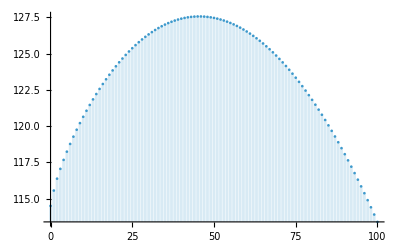

```mathematica
(*Log10 version*)
DiscretePlot[Log10[Sum[Binomial[k+1,2j+1]*(((1-j+2 k) Gamma[1+j+2 *100])/(Gamma[1+j-k+100] Gamma[2+k+100]))*(((2-j+2 k) Gamma[2+j+2 *100])/(Gamma[1+j-k+100] Gamma[3+k+100])),{j,0,Floor[k/2]}]],{k,0,100},PlotRange->All,GridLines->{{{2*Sqrt[2*100],Thick}},{}}]
```

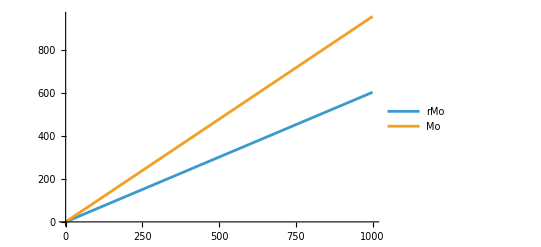

```mathematica
(*Comparison of RepGaps*)
Plot[{Log10[4^n],Log10[9^n]},{n,0,1000},PlotLegends->{"rMo","Mo"}]
```

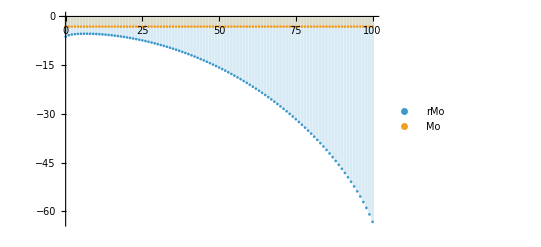

```mathematica
(*Direct comparison of ratios for n=100*)
DiscretePlot[{Log10[rightcell[100,k,0]/Sqrt[Sum[Sum[Binomial[k+1,2j+1]*(((1-j+2 k) Gamma[1+j+2 *100])/(Gamma[1+j-k+100] Gamma[2+k+100]))*(((2-j+2 k) Gamma[2+j+2 *100])/(Gamma[1+j-k+100] Gamma[3+k+100])),{j,0,Floor[k/2]}],{k,0,2*Sqrt[2*100]}]]],Log10[100^(-5/2)*3^(2*100)/Sqrt[3^(2*2*100+3/2)/(2^(5/2)*Sqrt[Pi]*(2*100)^(3/2))]]},{k,0,100},PlotLegends->{"rMo","Mo"}]
```